## Bootstrapped EWS plot for Fussmann system - Data From Hagrid

## Import data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* Job number *)
jobNum=6546;
```

```mathematica
(* Data directory *)
dataDir="hagrid/fussmann_ews/Jobs/job-"<>ToString[jobNum]<>"/"
```

hagrid/fussmann_ews/Jobs/job-6546/

```mathematica
(* Import parameters used *)
pars=Import[dataDir<>"pars.txt","Data"];
```

```mathematica
pars//TableForm
```

span | rw | ham_length | ham_offset | w_cutoff | sweep | block_size | bs_type | n_samples
80 | 1 | 80 | 0.5 | 1 | true | 40 | Circular | 100

```mathematica
(* EWS data *)
ewsRaw=Import[dataDir<>"ews_intervals.csv"];
```

### Bifurcation data

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

```mathematica
(* clear out points that go beyond max dilution rate on plot *)
bifPtsChlor=Table[DeleteCases[bifPtsChlor[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsChlor]}];
bifPtsBrach=Table[DeleteCases[bifPtsBrach[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsBrach]}];
```

### General figure parameters

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"];
imgs=400;
aratio=0.25;
padding={{60,60},{20,20}};
{{padLeft,padRight},{padBottom,padTop}}=padding;
lt=0.006;
colChlor=Darker[TMBcolours[[1]],0.15];
colBrach=Darker[TMBcolours[[4]],0.15];
{colChlor,colBrach}
labelPos=Scaled[{0.04,0.85}];
```

{RGBColor[0.31315445, 0.43076214999999995, 0.6033283],RGBColor[0.7841471, 0.3277821, 0.17780215]}

## Bifurcation diagram

```mathematica
deltaVals=Union[ewsRaw[[2;;,1]]]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

```mathematica
(* mark on approximate bifurcation points from experiment *)
expBif1a=0.32;
expBif1b=0.64;
expBif2=1.16;
expBifPts={expBif1a,expBif1b,expBif2};
```

```mathematica
(* chlorella bif *)
bifPlotChlorLines=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[lt]},{i,1,Length[bifPtsChlor]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
ImagePadding->padding,
Epilog->{EdgeForm[Directive[Darker[Green,0.4],Thickness[0.003]]],Opacity[0.05],Directive[Darker[Green,0.4]],Rectangle[{expBif1a,0},{expBif1b,4200000}],Opacity[1],Line[{{expBif2,0},{expBif2,4200000}}],Directive[{Black}],
Line[Table[{Scaled[{0,-0.05},{deltaVals[[i]],0}],
Scaled[{0,0.05},{deltaVals[[i]],0}]},{i,1,Length[deltaVals]}]],
Directive[{Black}],Text[Style["a",14,Bold],Scaled[{0.04,0.9}]]}]
```

-Graphics-

```mathematica
bifPlotChlor=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[lt]},{i,1,Length[bifPtsChlor]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
ImagePadding->padding,
Epilog->{Directive[{Black}],
Line[Table[{Scaled[{0,-0.05},{deltaVals[[i]],0}],
Scaled[{0,0.05},{deltaVals[[i]],0}]},{i,1,Length[deltaVals]}]],
Directive[{Black}],Text[Style["a",14,Bold],Scaled[{0.04,0.9}]]}]
```

-Graphics-

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,1.5},{-59/40,59}},
PlotStyle->Table[{colBrach,Thickness[lt]},{i,1,Length[bifPtsBrach]}],
LabelStyle->14,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlor. (10^6 cells/ml)",White],"Brach. (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
ImagePadding->padding];
```

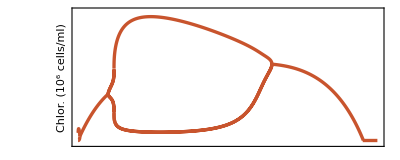
-Graphics--Graphics-

```mathematica
(* put together *)
bifPlot=Overlay[{bifPlotChlor,bifPlotBrach}]
```

## Plots of EWS against delta

```mathematica
ewsRaw[[1]]
```

{Dilution rate,Species,,Variance,Lag-1 AC,Lag-2 AC,Lag-10 AC,AIC fold,AIC hopf,AIC null,Smax}

### Variance

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"Variance"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

```mathematica
varPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
Filling->{{3->{1},3->{2}}},
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{Range[0,1,0.2],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos]}
];
```

```mathematica
varPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Var"},{"",""}},
FrameTicks->{{None,Range[0,50,10]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

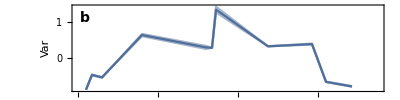

```mathematica
varPlotComp=ListLinePlot[{lowerSeriesComp,upperSeriesComp,meanSeriesComp},
LabelStyle->14,
Filling->{{3->{1},3->{2}}},
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Frame->{{True,True},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{All,Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos]}]
```

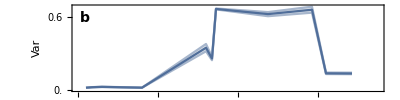
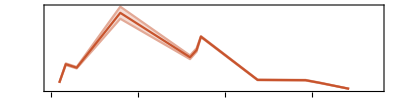

```mathematica
varPlot=Overlay[{varPlotChlor,varPlotBrach}]
```

### Variance log plot

```mathematica
varPlotChlorLog=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{10^(-2.5),2}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{{{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos]}
];
```

```mathematica
varPlotBrachLog=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{10^(-1),200}},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Var"},{"",""}},
FrameTicks->{{None,{{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,1},{10,10},{100,100}}},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

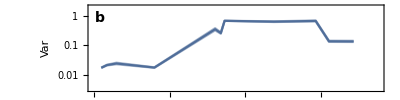
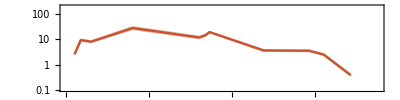

```mathematica
varPlotLog=Overlay[{varPlotChlorLog,varPlotBrachLog}]
```

### Coefficient of variation ( to be computed )

### Lag-1 AC

```mathematica
ewsIndex=Position[ewsRaw[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

```mathematica
acPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-1 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Filling->{{3->{1},3->{2}}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-1 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

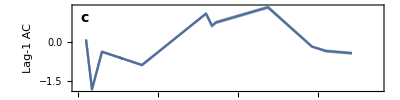

```mathematica
ac1PlotComp=ListLinePlot[{lowerSeriesComp,upperSeriesComp,meanSeriesComp},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"Lag-1 AC",""},{"",""}},
FrameTicks->{{All,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}]
```

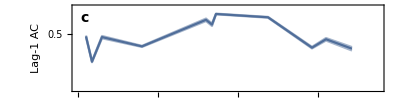
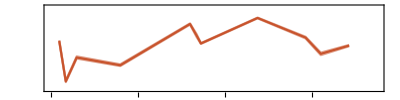

```mathematica
ac1Plot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Lag-2 AC

```mathematica
ewsIndex=Position[ewsRaw[[1]],"Lag-2 AC"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

```mathematica
acPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-2 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Filling->{{3->{1},3->{2}}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-2 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

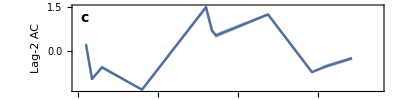

```mathematica
ac2PlotComp=ListLinePlot[{lowerSeriesComp,upperSeriesComp,meanSeriesComp},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"Lag-2 AC",""},{"",""}},
FrameTicks->{{All,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}]
```

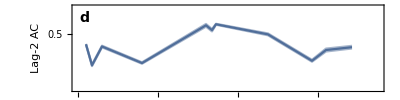
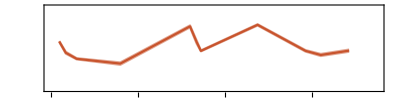

```mathematica
ac2Plot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Lag-10 AC

```mathematica
ewsIndex=Position[ewsRaw[[1]],"Lag-10 AC"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

```mathematica
acPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,0.5}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-10 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,0.5}},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Filling->{{3->{1},3->{2}}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-10 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

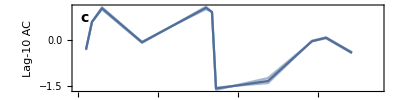

```mathematica
ac10PlotComp=ListLinePlot[{lowerSeriesComp,upperSeriesComp,meanSeriesComp},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"Lag-10 AC",""},{"",""}},
FrameTicks->{{All,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}]
```

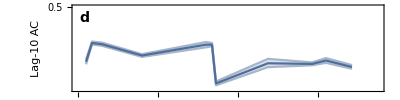
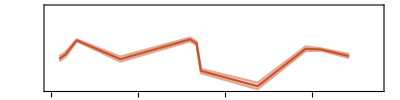

```mathematica
ac10Plot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Smax

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"Smax"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

```mathematica
smaxPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
Filling->{{3->{1},3->{2}}},
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Frame->{{True,False},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{Range[0,10,0.1],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}
];
```

```mathematica
smaxPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","S_max"},{"",""}},
FrameTicks->{{None,Range[0,10,1]//N},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

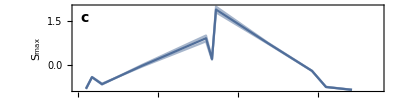

```mathematica
smaxPlotComp=ListLinePlot[{lowerSeriesComp,upperSeriesComp,meanSeriesComp},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{All,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}]
```

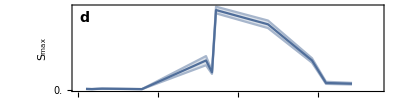
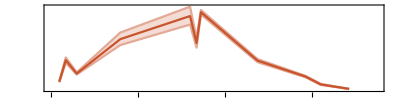

```mathematica
smaxPlot=Overlay[{smaxPlotChlor,smaxPlotBrach}]
```

### Smax Log Scale

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"Smax"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
smaxPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
ScalingFunctions->"Log",
LabelStyle->14,
Filling->{{3->{1},3->{2}}},
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Frame->{{True,False},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{{{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}
];
```

```mathematica
smaxPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
ScalingFunctions->"Log",
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},All},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","S_max"},{"",""}},
FrameTicks->{{None,{{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}}},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

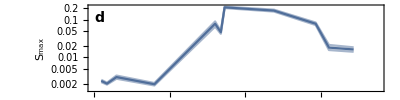
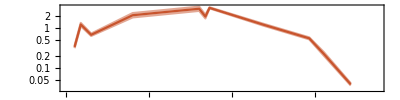

```mathematica
smaxPlotLog=Overlay[{smaxPlotChlor,smaxPlotBrach}]
```

### AIC weight fold

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"AIC fold"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{lowerSeriesB[[;;,2]],lowerSeriesC[[;;,2]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{upperSeriesB[[;;,2]],upperSeriesC[[;;,2]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{meanSeriesB[[;;,2]],meanSeriesC[[;;,2]]}]}];
```

```mathematica
aicfoldPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_fold",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{50,padTop}},
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

```mathematica
aicfoldPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_fold"},{"",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

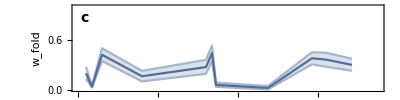

```mathematica
aicFoldPlotComp=ListLinePlot[{lowerSeriesComp,upperSeriesComp,meanSeriesComp},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,1}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"w_fold",""},{"",""}},
FrameTicks->{{All,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}]
```

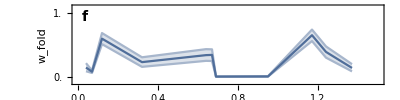
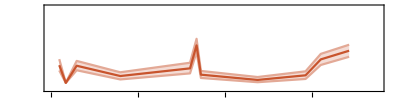

```mathematica
aicFoldPlot=Overlay[{aicfoldPlotChlor,aicfoldPlotBrach}]
```

### AIC weight Hopf

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"AIC hopf"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{lowerSeriesB[[;;,2]],lowerSeriesC[[;;,2]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{upperSeriesB[[;;,2]],upperSeriesC[[;;,2]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{meanSeriesB[[;;,2]],meanSeriesC[[;;,2]]}]}];
```

```mathematica
aicfoldPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_hopf",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Text[Style["e",14,Bold],labelPos]}];
```

```mathematica
aicfoldPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_hopf"},{"",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

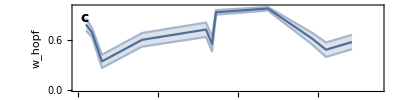

```mathematica
aicHopfPlotComp=ListLinePlot[{lowerSeriesComp,upperSeriesComp,meanSeriesComp},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,1}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"w_hopf",""},{"",""}},
FrameTicks->{{All,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}]
```

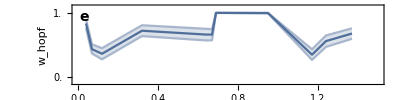
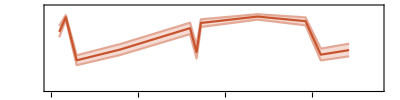

```mathematica
aicHopfPlot=Overlay[{aicfoldPlotChlor,aicfoldPlotBrach}]
```

### AIC weight Null

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"AIC null"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{lowerSeriesB[[;;,2]],lowerSeriesC[[;;,2]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{upperSeriesB[[;;,2]],upperSeriesC[[;;,2]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{meanSeriesB[[;;,2]],meanSeriesC[[;;,2]]}]}];
```

```mathematica
aicfoldPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_null",""},{"",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

```mathematica
aicfoldPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->14,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{Lighter[colBrach,0.5],Lighter[colBrach,0.5],colBrach},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_null"},{"",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

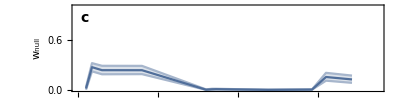

```mathematica
aicNullPlotComp=ListLinePlot[{lowerSeriesComp,upperSeriesComp,meanSeriesComp},
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,1}},
PlotStyle->{Lighter[colChlor,0.5],Lighter[colChlor,0.5],colChlor},
Filling->{{3->{1},3->{2}}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"w_null",""},{"",""}},
FrameTicks->{{All,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}]
```

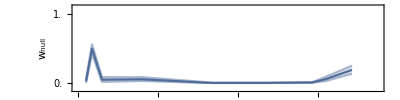
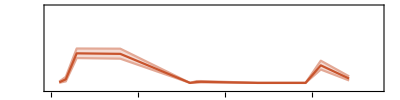

```mathematica
aicNullPlot=Overlay[{aicfoldPlotChlor,aicfoldPlotBrach}]
```

## Grid all plots together

```mathematica
plotTemp=Grid[{{bifPlot},{varPlot},{ac1Plot},{smaxPlot},{aicHopfPlot}},Spacings->{0,-1.5}];
```

```mathematica
lHeight1=0.148;
lHeight2=2.931;
```

```mathematica
ewsFussmannPlot=Overlay[{plotTemp,
Graphics[{(*EdgeForm[Directive[Darker[Green,0.5],Thickness[0.003]]]*)
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{expBif1a,lHeight1},{expBif1b,lHeight2}],
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{expBif2-0.01,lHeight1},{expBif2+0.01,lHeight2}]},
ImageSize->400,AspectRatio->1.6,Frame->True,
FrameStyle->Directive[Opacity[0]],
PlotRange->{{-0.225,1.805},{0,3}}]}];
```

```mathematica
(*Export["figures/fussmann_ews_bootstrap1.png",ewsFussmannPlot,ImageResolution->200];*)
```

### Log version

```mathematica
plotTemp=Grid[{{bifPlot},{varPlotLog},{ac1Plot},{smaxPlotLog},{aicHopfPlot},{aicFoldPlot}},Spacings->{0,-1.5}];
```

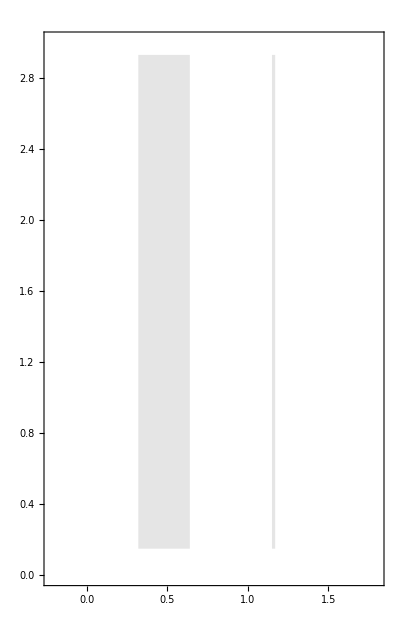
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
ewsFussmannPlotLog=Overlay[{plotTemp,
Graphics[{(*EdgeForm[Directive[Darker[Green,0.5],Thickness[0.003]]]*)
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{expBif1a,lHeight1},{expBif1b,lHeight2}],
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{expBif2-0.01,lHeight1},{expBif2+0.01,lHeight2}]},
ImageSize->400,AspectRatio->1.6,Frame->True,
FrameStyle->Directive[Opacity[0]],
PlotRange->{{-0.225,1.805},{0,3}}]}]
```

```mathematica
Export["figures/ews_bootstrap/hagrid_sess2/job"<>ToString[jobNum]<>"_ews.png",ewsFussmannPlotLog,ImageResolution->100];
```

### Composite version

```mathematica
plotTemp=Grid[{{bifPlot},{varPlotComp},{ac1PlotComp},{smaxPlotComp},{aicHopfPlotComp},{aicFoldPlotComp}},Spacings->{0,-1.5}];
```

```mathematica
ewsFussmannPlotLog=Overlay[{plotTemp,
Graphics[{(*EdgeForm[Directive[Darker[Green,0.5],Thickness[0.003]]]*)
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{expBif1a,lHeight1},{expBif1b,lHeight2}],
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{expBif2-0.01,lHeight1},{expBif2+0.01,lHeight2}]},
ImageSize->400,AspectRatio->1.6,Frame->True,
FrameStyle->Directive[Opacity[0]],
PlotRange->{{-0.225,1.805},{0,3}}]}];
```